Se presenta gráficas de los índices de refracción de datos experimentales obtenidos de https://refractiveindex.info/ para diversos materiales

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
Needs["MaTeX`"]
```

### Oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ℏωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kAu=kau1[[All,2]];
nAu=nau+ I kAu;
h c/hbarraomegaAu
```

{195.3,199.3,203.3,207.3,211.9,216.4,221.4,226.2,231.3,237.1,242.6,249.,255.1,261.6,268.9,276.1,284.4,292.4,300.9,310.7,320.4,331.5,342.5,354.2,367.9,381.5,397.4,413.3,430.5,450.9,471.4,495.9,520.9,548.6,582.1,616.8,659.5,704.5,756.,821.1,892.,984.,1088.,1216.,1393.,1610.,1937.}

```mathematica
hbarraomegaAu=Drop[ℏωAu,{1,2}];
epsReal=1-Re[Drop[nAu,{1,2}]^2];
epsImag=Im[Drop[nAu,{1,2}]^2]*10;
```

```mathematica
auReal = Interpolation[Transpose[{hbarraomegaAu,epsReal}]]
auImag = Interpolation[Transpose[{hbarraomegaAu,epsImag}]];
```

InterpolatingFunction[…]

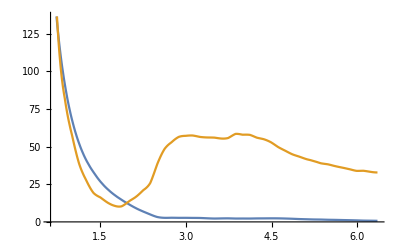

```mathematica
Plot[{auReal [x],auImag[x]},{x,0.641,6.35}]
```

```mathematica
h c/1
```

1240.7

```mathematica
upperTicks4=Module[{labels,positions},labels={207,248,310,414,620,1240};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

```mathematica
drudeAuInterpo=Plot[{Style[auReal [x],Blue,Thickness[0.003]],Style[auImag[x],Red,Thickness[0.003]]},{x,0.641,6.35},PlotRange->All];
```

```mathematica
drudeAupoints=ListPlot[{Style[auReal ,Blue],Style[auImag,Red]},PlotRange->All];
```

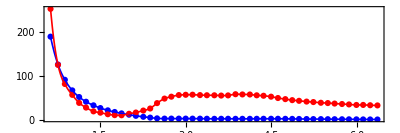

```mathematica
drudeAu=Show[{drudeAupoints,drudeAuInterpo},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],PlotMarkers->{•},PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},
FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,AspectRatio->1/3]
```

```mathematica
Export["drudeAu.svg",drudeAu]
```

drudeAu.svg

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en um*)
ℏωAg=h c/λAg; (*eV*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
hbarraomegaAg0=Drop[ℏωAg,{1,20}];
hbarraomegaAg=Drop[hbarraomegaAg0,{-13,-1}];
nAggg=Drop[nAgg,{1,20}];
epsRealAg=1-Re[Drop[nAggg,{-13,-1}]^2];
epsImagAg=Im[Drop[nAggg,{-13,-1}]^2]*10;
```

```mathematica
agReal = Interpolation[Transpose[{hbarraomegaAg,epsRealAg}]];
agImag = Interpolation[Transpose[{hbarraomegaAg,epsImagAg}]];
```

```mathematica
h c/2.5
```

496.28

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

```mathematica
drudeAgInterpo=Plot[{Style[agReal [x],Blue,Thickness[0.003]],Style[agImag[x],Red,Thickness[0.003]]},{x,2.262,4.12},PlotRange->All];
```

```mathematica
drudeAgpoints=ListPlot[{Style[agReal ,Blue],Style[agImag,Red]},PlotRange->All];
```

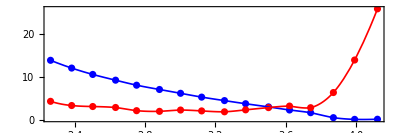

```mathematica
drudeAg=Show[{drudeAgpoints,drudeAgInterpo},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],PlotMarkers->{•},PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},
FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,AspectRatio->1/3]
```

```mathematica
Export["drudeAg.svg",drudeAg]
```

drudeAg.svg

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
bism=Import["C:\\Users\\Lunita\\OneDrive\\Documentos\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

Import::nffil: File C:\Users\Lunita\OneDrive\Documentos\GitHub\Servicio-Social\Notebooks Mathematica\Funciones dieléctricas\Bismuto Hagemann.csv not found during Import.

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
ℏωBism=h c/λBism; (*eV*)
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
hbarraomegaBi=Drop[Drop[ℏωBism,{1,139}],{-3,-1}];
epsRealBi=1-Drop[Re[Drop[nBismuto,{1,139}]^2],{-3,-1}];
epsImagBi=Drop[Im[Drop[nBismuto,{1,139}]^2],{-3,-1}];
```

```mathematica
biReal = Interpolation[Transpose[{hbarraomegaBi,epsRealBi}]]
biImag = Interpolation[Transpose[{hbarraomegaBi,epsImagBi}]];
```

InterpolatingFunction[…]

```mathematica
drudeBiInterpo=Plot[{Style[biReal [x],Blue,Thickness[0.003]],Style[biImag[x],Red,Thickness[0.003]]},{x,0.81,4},PlotRange->All];
```

```mathematica
drudeBipoints=ListPlot[{Style[biReal ,Blue],Style[biImag,Red]},PlotRange->All];
```

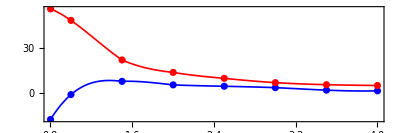

```mathematica
drudeBi=Show[{drudeBipoints,drudeBiInterpo},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],PlotMarkers->{•},PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},
FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,AspectRatio->1/3]
```

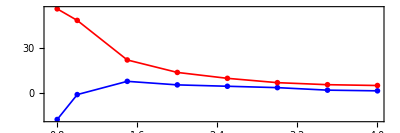

```mathematica
drudeBi=ListLinePlot[{Style[biReal ,Blue],Style[biImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},
FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,AspectRatio->1/3]
```

```mathematica
Export["drudeBi.svg",drudeBi]
```

drudeBi.svg

```mathematica
h c/(5*10^(8))
```

2.4814×10^-6

```mathematica
upperTicks4=Module[{labels,positions},labels={2.5*^-6,3.1*^-6,4.1*^-6,6.2*^-6,1.24*10^(-5)};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

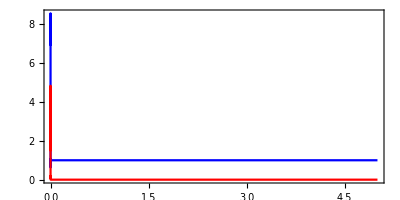

```mathematica
bis=ListLinePlot[{Style[Transpose[{ℏωBism,nBis}],Blue],Style[Transpose[{ℏωBism,kBis}],Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["n,k"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["n"],MaTeX["k "]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}],AspectRatio->1/2]
```

```mathematica
Export["Bisexp.svg",bis]
```

Bisexp.svg

### Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000;(*λ en um*)
ℏωMgO=2 Pi c ℏ/λMgO; (*eV*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
λMgO
```

{360.,410.4,460.8,511.2,561.6,612.,662.4,712.8,763.2,813.6,864.,914.4,964.8,1015.,1066.,1116.,1166.,1217.,1267.,1318.,1368.,1418.,1469.,1519.,1570.,1620.,1670.,1721.,1771.,1822.,1872.,1922.,1973.,2023.,2074.,2124.,2174.,2225.,2275.,2326.,2376.,2426.,2477.,2527.,2578.,2628.,2678.,2729.,2779.,2830.,2880.,2930.,2981.,3031.,3082.,3132.,3182.,3233.,3283.,3334.,3384.,3434.,3485.,3535.,3586.,3636.,3686.,3737.,3787.,3838.,3888.,3938.,3989.,4039.,4090.,4140.,4190.,4241.,4291.,4342.,4392.,4442.,4493.,4543.,4594.,4644.,4694.,4745.,4795.,4846.,4896.,4946.,4997.,5047.,5098.,5148.,5198.,5249.,5299.,5350.,5400.}

```mathematica
hbarraomegaMgO=Drop[ℏωMgO,{-95,-1}];
epsRealMgO=1-Re[Drop[nMgO,{-95,-1}]^2];
epsImagMgO=Im[Drop[nMgO,{-95,-1}]^2];
```

```mathematica
mgOReal = Interpolation[Transpose[{hbarraomegaMgO,epsRealMgO}]]
mgOImag = Interpolation[Transpose[{hbarraomegaMgO,epsImagMgO}]];
```

InterpolatingFunction[…]

```mathematica
upperTicksMgO=Module[{labels,positions},labels={365,388,413,443,477,516,564,620};
positions=h c/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorMgO=Module[{labels,positions,size},labels={};
positions=h c/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

```mathematica
drudeMgOInterpo=Plot[{Style[mgOReal [x],Blue,Thickness[0.003]],Style[mgOImag[x],Red,Thickness[0.003]]},{x,2.03,3.45},PlotRange->All];
```

```mathematica
drudeMgOpoints=ListPlot[{Style[mgOReal ,Blue],Style[mgOImag,Red]},PlotRange->All];
```

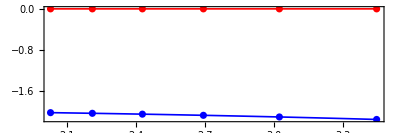

```mathematica
drudeMgO=Show[{drudeMgOpoints,drudeMgOInterpo},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],PlotMarkers->{•},PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},
FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,AspectRatio->1/3]
```

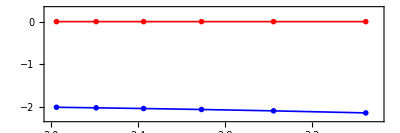

```mathematica
drudeMgO=ListLinePlot[{Style[mgOReal ,Blue],Style[mgOImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],PlotMarkers->{•},Joined->True,PlotStyle->{Thickness[0.003]},PlotRange->{{2,3.5},{-2.3,0.3}},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.6],None},{Style[MaTeX["\hbar\omega \:[\mbox{eV}]"],Magnification->1.6],Style[MaTeX["\lambda\:[\mbox{nm}]"],Magnification->1.6]}},LabelStyle->{FontFamily->"CMU Serif"},
FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,AspectRatio->1/3]
```

```mathematica
Export["drudeMgO.svg",drudeMgO]
```

drudeMgO.svg

### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]];
ℏωalum=2 Pi c ℏ/λalum; (*eV*)
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
```

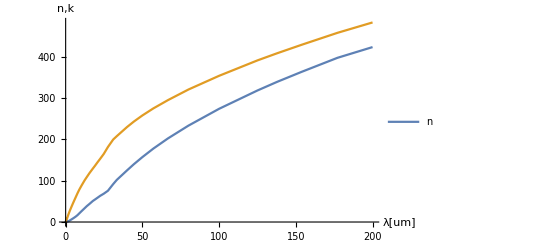

```mathematica
ListLinePlot[{Transpose[{λalum,nalum}],Transpose[{λalum,kalum}]},PlotRange->All,AxesLabel->{"λ[um]","n,k"},PlotLegends->{"n"}]
```

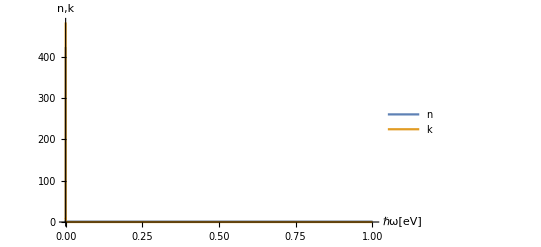

```mathematica
ListLinePlot[{Transpose[{ℏωalum,nalum}],Transpose[{ℏωalum,kalum}]},PlotRange->All,AxesLabel->{"ℏω[eV]","n,k"},PlotLegends->{"n","k"}]
```

```mathematica
h c/350
```

3.54486

```mathematica
ϵℏω[ℏω_,ℏωp_,ℏγ_]:=1-((ℏωp/ℏ)^2/((ℏω/ℏ)((ℏω/ℏ)+ I * (ℏγ/ℏ))))(*recibe en eV*)
```

```mathematica
alReal=Table[{ℏω,1-Re[ϵℏω[ℏω,13.142,0.197]]},{ℏω,3.5448580251428568,9.9256024704,0.01}];
alImag=Table[{ℏω,Im[ϵℏω[ℏω,13.142,0.197]*20]},{ℏω,3.5448580251428568,9.9256024704,0.01}];
```

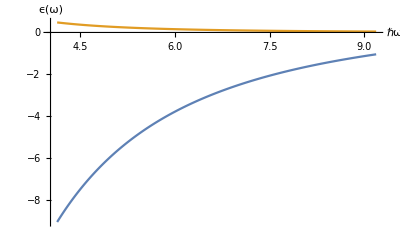

```mathematica
ListLinePlot[{alReal,alImag},AxesLabel->{"ℏω","ϵ(ω)"}]
```

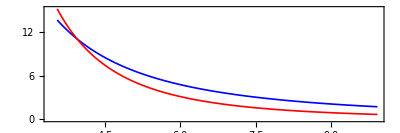

```mathematica
drudeAl=ListPlot[{Style[alReal ,Blue],Style[alImag,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],Joined->True,PlotStyle->{Thickness[0.003]},
FrameLabel->{{Style[MaTeX["\mbox{Re}[\epsilon (\omega)] "],Magnification->1.6],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.6],None}},LabelStyle->{FontFamily->"CMU Serif"},FrameTicks->{{All,None},{Automatic,None}},PlotRange->All,AspectRatio->1/3]
```

```mathematica
Export["drudeAl.svg",drudeAl]
```

drudeAl.svg